```mathematica
ff[z_]= d0 z Log[z]+d1 z+d2 z^2 Log[z]^2+d3 z^2 Log[z]+d4 z^2;
Collect[PowerExpand[Series[ff[z]-g (Exp[ z/g+ff[z/g]] -1),{z,0,2}]],z]
```

z (-1+d0 Log[g])+1/(2 g)z^2 (-1-2 d1-d1^2-2 d4+2 d4 g+2 d0 Log[g]+2 d0 d1 Log[g]+2 d3 Log[g]-d0^2 Log[g]^2-2 d2 Log[g]^2-2 d0 Log[z]-2 d0 d1 Log[z]-2 d3 Log[z]+2 d3 g Log[z]+2 d0^2 Log[g] Log[z]+4 d2 Log[g] Log[z]-d0^2 Log[z]^2-2 d2 Log[z]^2+2 d2 g Log[z]^2)

```mathematica
Collect[-1-2 d1-d1^2-2 d4+2 d4 g+2 d0 Log[g]+2 d0 d1 Log[g]+2 d3 Log[g]-d0^2 Log[g]^2-2 d2 Log[g]^2-2 d0 Log[z]-2 d0 d1 Log[z]-2 d3 Log[z]+2 d3 g Log[z]+2 d0^2 Log[g] Log[z]+4 d2 Log[g] Log[z]-d0^2 Log[z]^2-2 d2 Log[z]^2+2 d2 g Log[z]^2,Log[z]]
```

-1-2 d1-d1^2-2 d4+2 d4 g+2 d0 Log[g]+2 d0 d1 Log[g]+2 d3 Log[g]-d0^2 Log[g]^2-2 d2 Log[g]^2+(-2 d0-2 d0 d1-2 d3+2 d3 g+2 d0^2 Log[g]+4 d2 Log[g]) Log[z]+(-d0^2-2 d2+2 d2 g) Log[z]^2

```mathematica
Solve[-d0^2-2 d2+2 d2 g==0,d2]
```

{{d2→d0^2/(2 (-1+g))}}

```mathematica
Solve[-2 d0-2 d0 d1-2 d3+2 d3 g+2 d0^2 Log[g]+4 d2 Log[g]==0,d3,Assumptions->{d2==d0^2/(2 (-1+g))}]
```

{{d3→(d0+d0 d1-d0^2 Log[g]-2 d2 Log[g])/(-1+g)}}

```mathematica
FullSimplify[Solve[-1-2 d1-d1^2-2 d4+2 d4 g+2 d0 Log[g]+2 d0 d1 Log[g]+2 d3 Log[g]-d0^2 Log[g]^2-2 d2 Log[g]^2==0,d4]//. {d3->(d0+d0 d1-d0^2 Log[g]-2 d2 Log[g])/(-1+g),d2->d0^2/(2 (-1+g)),d0->1/Log[g]}]
```

{{d4→(1+d1 (-2+d1 (-1+g)) (-1+g)+g)/(2 (-1+g)^3)}}

```mathematica
Collect[FullSimplify[FullSimplify[FullSimplify[ 1/(1-g) +1/Log[g]+2 d2 ep Log[ep]^2+(2 d2 + 2d3 )ep Log[ep]+(d3+2 d4)ep]//.{d4->(1+2 d1+d1^2-2 d0 Log[g]-2 d0 d1 Log[g]-2 d3 Log[g]+d0^2 Log[g]^2+2 d2 Log[g]^2)/(2 (-1+g)),d3->(d0+d0 d1-d0^2 Log[g]-2 d2 Log[g])/(-1+g),d2->d0^2/(2 (-1+g)),d0->1/Log[g]}]/.{d1->1/(1-g)+g(1-g)-Log[ep]/Log[g]}],ep]
```

(-((1-g) (-1+g)^2)-(-1+g)^2 Log[g])/((-1+g)^3 Log[g])+(ep ((1-g) (2+(-1+g)^2 g)+(4+g (5-7 g+g^3 (6+(-4+g) g))) Log[g]))/((-1+g)^3 Log[g])

```mathematica
Solve[ep == (-((1-g) (-1+g)^2)-(-1+g)^2 Log[g])/((-1+g)^3 Log[g])+(ep ((1-g) (2+(-1+g)^2 g)+(4+g (5-7 g+g^3 (6+(-4+g) g))) Log[g]))/((-1+g)^3 Log[g]),ep]
```

{{ep→(-((1-g) (-1+g)^2)-(-1+g)^2 Log[g])/((-1+g)^3 Log[g] (1-((1-g) (2+(-1+g)^2 g)+(4+g (5-7 g+g^3 (6+(-4+g) g))) Log[g])/((-1+g)^3 Log[g])))}}

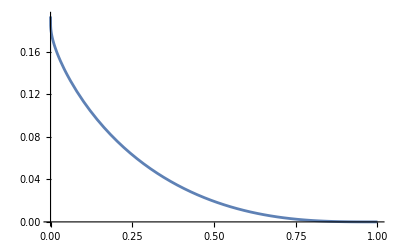

```mathematica
Plot[(-((1-g) (-1+g)^2)-(-1+g)^2 Log[g])/((-1+g)^3 Log[g] (1-((1-g) (2+(-1+g)^2 g)+(4+g (5-7 g+g^3 (6+(-4+g) g))) Log[g])/((-1+g)^3 Log[g]))),{g,0,1}]
```

```mathematica
FullSimplify[1/(1-g)+g(1-g)-Log[(-((1-g) (-1+g)^2)-(-1+g)^2 Log[g])/((-1+g)^3 Log[g] (1-((1-g) (2+(-1+g)^2 g)+(4+g (5-7 g+g^3 (6+(-4+g) g))) Log[g])/((-1+g)^3 Log[g])))]/Log[g]]
```

1/(1-g)+g-g^2-Log[-((-1+g)^2 (-1+g-Log[g]))/(-((-1+g) (2+(-1+g)^2 g))+(5+(-1+g) g (-2+g (2+g (3+(-3+g) g)))) Log[g])]/Log[g]

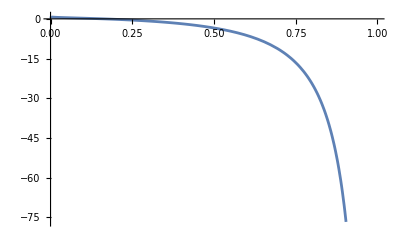

```mathematica
Plot[1/(1-g)+g-g^2-Log[-((-1+g)^2 (-1+g-Log[g]))/(-((-1+g) (2+(-1+g)^2 g))+(5+(-1+g) g (-2+g (2+g (3+(-3+g) g)))) Log[g])]/Log[g],{g,0,1}]
```

```mathematica
FullSimplify[(ep ((4+g (5-7 g+g^3 (6+(-4+g) g))) ))/(-1+g)^3]
```

(ep (4+g (5-7 g+g^3 (6+(-4+g) g))))/(-1+g)^3

```mathematica
Solve[f^2(1/g-1)ep+f (2/g-1)ep+1-g+ep/g==0,f]
```

{{f→(ep-(2 ep)/g-(√ep √(-4+8 g+ep g-4 g^2))/(√g))/(2 (-ep+ep/g))},{f→(ep-(2 ep)/g+(√ep √(-4+8 g+ep g-4 g^2))/(√g))/(2 (-ep+ep/g))}}

```mathematica
Solve[(ep-(2 ep)/g-(√ep √(-4+8 g+ep g-4 g^2))/(√g))/(2 (-ep+ep/g)) == g(1-g)+(-((1-g) (-1+g)^2)-(-1+g)^2 Log[g])/((-1+g)^3 Log[g]),ep]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ep→-(((-1+g)^2 g Log[g]^2)/(1-2 g+g^2+4 Log[g]-3 g Log[g]-5 g^2 Log[g]+6 g^3 Log[g]-2 g^4 Log[g]+4 Log[g]^2+2 g Log[g]^2-8 g^2 Log[g]^2+2 g^3 Log[g]^2+5 g^4 Log[g]^2-4 g^5 Log[g]^2+g^6 Log[g]^2))}}

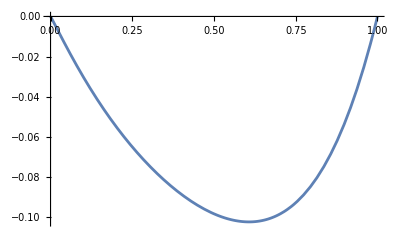

```mathematica
Plot[-(((-1+g)^2 g Log[g]^2)/(1-2 g+g^2+4 Log[g]-3 g Log[g]-5 g^2 Log[g]+6 g^3 Log[g]-2 g^4 Log[g]+4 Log[g]^2+2 g Log[g]^2-8 g^2 Log[g]^2+2 g^3 Log[g]^2+5 g^4 Log[g]^2-4 g^5 Log[g]^2+g^6 Log[g]^2)),{g,0,1}]
```

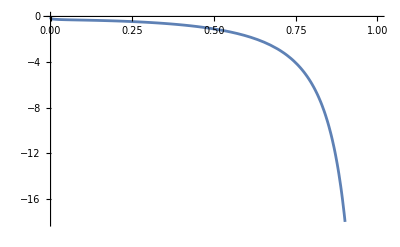

```mathematica
Plot[1/(1-g)+g(1-g)-Log[Abs[-(((-1+g)^2 g Log[g]^2)/(1-2 g+g^2+4 Log[g]-3 g Log[g]-5 g^2 Log[g]+6 g^3 Log[g]-2 g^4 Log[g]+4 Log[g]^2+2 g Log[g]^2-8 g^2 Log[g]^2+2 g^3 Log[g]^2+5 g^4 Log[g]^2-4 g^5 Log[g]^2+g^6 Log[g]^2))]]/Log[g],{g,0,1}]
```

```mathematica
Sum[z^n/(a^n n! (ca ^(n-1)-1)),{n,2,Infinity}]
```

∑_(n=2)^∞ (a^-n z^n)/((-1+ca^(-1+n)) n!)

```mathematica
ff[z_]= d0 z Log[z]+d1 z+d2 z^2 Log[z]^2+d3 z^2 Log[z]+d4 z^2;
Collect[PowerExpand[Series[ff[z]-z-g (Exp[ ff[z/g]] -1),{z,0,2}]],z]
```

z (-1+d0 Log[g])+1/(2 g)z^2 (-d1^2-2 d4+2 d4 g+2 d0 d1 Log[g]+2 d3 Log[g]-d0^2 Log[g]^2-2 d2 Log[g]^2-2 d0 d1 Log[z]-2 d3 Log[z]+2 d3 g Log[z]+2 d0^2 Log[g] Log[z]+4 d2 Log[g] Log[z]-d0^2 Log[z]^2-2 d2 Log[z]^2+2 d2 g Log[z]^2)

```mathematica
Collect[-d1^2-2 d4+2 d4 g+2 d0 d1 Log[g]+2 d3 Log[g]-d0^2 Log[g]^2-2 d2 Log[g]^2-2 d0 d1 Log[z]-2 d3 Log[z]+2 d3 g Log[z]+2 d0^2 Log[g] Log[z]+4 d2 Log[g] Log[z]-d0^2 Log[z]^2-2 d2 Log[z]^2+2 d2 g Log[z]^2,Log[z]]
```

-d1^2-2 d4+2 d4 g+2 d0 d1 Log[g]+2 d3 Log[g]-d0^2 Log[g]^2-2 d2 Log[g]^2+(-2 d0 d1-2 d3+2 d3 g+2 d0^2 Log[g]+4 d2 Log[g]) Log[z]+(-d0^2-2 d2+2 d2 g) Log[z]^2

```mathematica
Solve[(-d0^2-2 d2+2 d2 g==0),d2]/.{d0->1/Log[g]}
```

{{d2→1/(2 (-1+g) Log[g]^2)}}

```mathematica
Solve[-2 d0 d1-2 d3+2 d3 g+2 d0^2 Log[g]+4 d2 Log[g]==0,d3]//.{d2->1/(2 (-1+g) Log[g]^2),d0->1/Log[g]}
```

{{d3→(-1/Log[g]+d1/Log[g]-1/((-1+g) Log[g]))/(-1+g)}}

```mathematica
FullSimplify[Solve[-d1^2-2 d4+2 d4 g+2 d0 d1 Log[g]+2 d3 Log[g]-d0^2 Log[g]^2-2 d2 Log[g]^2==0,d4]//.{d2->1/(2 (-1+g) Log[g]^2),d0->1/Log[g],d3->(-1/Log[g]+d1/Log[g]-1/((-1+g) Log[g]))/(-1+g)}]
```

```mathematica
(d0+d0 d1-d0^2 Log[g]-2 d2 Log[g])/(-1+g)/.{d0->1/Log[g]}
```

```mathematica
(d1/Log[g]-2 d2 Log[g])/(-1+g)/.{d2->1/(2 (-1+g) Log[g]^2)}
```

```mathematica
-(d1/Log[g]-1/((-1+g) Log[g]))/(-1+g)+2 f 1/(2 (-1+g) Log[g]^2)
```

-(d1/Log[g]-1/((-1+g) Log[g]))/(-1+g)+f/((-1+g) Log[g]^2)

```mathematica
FullSimplify[-f(-(d1/Log[g]-1/((-1+g) Log[g]))/(-1+g)+f/((-1+g) Log[g]^2))+1/(2 (-1+g) Log[g]^2)f^2-1/Log[g]-(1/(-1+g)+f^2/Log[g]^2+(2 (f/Log[g]^2-1/((-1+g) Log[g])) Log[g])/(-1+g))/(2 (-1+g))]
```

-(2 f^2 (-1+g)^2+2 (-1+g) ((-1+g)^2+f (2+d1-d1 g)) Log[g]+(-3+g) Log[g]^2)/(2 (-1+g)^3 Log[g]^2)

```mathematica
(1+2 d1+d1^2-2 d0 Log[g]-2 d0 d1 Log[g]-2 d3 Log[g]+d0^2 Log[g]^2+2 d2 Log[g]^2)/(2 (-1+g))//.{d0-> 1/Log[g],d1->f/Log[g],d3->-(d1/Log[g]-1/((-1+g) Log[g]))/(-1+g),d2->1/(2 (-1+g) Log[g]^2)}
```

```mathematica
(1/(-1+g)+f^2/Log[g]^2+(2 (f/Log[g]^2-1/((-1+g) Log[g])) Log[g])/(-1+g))/(2 (-1+g))
```

```mathematica
ψ[z]= -g Exp[-g+z];
PowerExpand[Series[-g/z-ProductLog[ -g Exp[-g+z/g]]Exp[ProductLog[ -g Exp[-g+z/g]]-ProductLog[ -g Exp[-g+z/g^2]]Exp[ProductLog[ -g Exp[-g+z/g^2]]-ProductLog[ -g Exp[-g+z/g^3]]Exp[ProductLog[ -g Exp[-g+z/g^3]]-ProductLog[ -g Exp[-g+z/g^4]]]]]/z,{z,0,0}]]
```

(ⅇ^-g (4 ⅇ^g g-3 ⅇ^g g^2))/((1-g) g)+O[z]^1

```mathematica
FullSimplify[PowerExpand[Series[(-g-ProductLog[ -g Exp[-g+z/g]]Exp[ProductLog[ -g Exp[-g+z/g]]-ProductLog[ -g Exp[-g+z/g^2]]Exp[ProductLog[ -g Exp[-g+z/g^2]]-ProductLog[ -g Exp[-g+z/g^3]]Exp[ProductLog[ -g Exp[-g+z/g^3]]-ProductLog[ -g Exp[-g+z/g^4]]]]])/z,{z,0,0}]]]
```

(3+1/(1-g))+O[z]^1

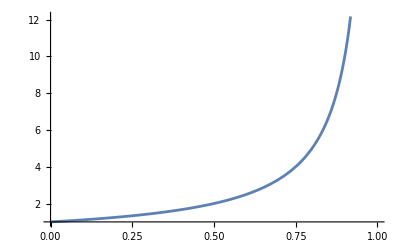

```mathematica
Plot[1/(1-g),{g,0,1}]
```

```mathematica
FullSimplify[PowerExpand[Limit[t(-g-ProductLog[ -g Exp[-g+1/(t g)]])+Log[t],t->Infinity]]]
```

ComplexInfinity

```mathematica
FullSimplify[PowerExpand[Series[t(-g-ProductLog[ -g Exp[-g+1/(t g)]]Exp[ProductLog[ -g Exp[-g+1/(t g)]]-ProductLog[ -g Exp[-g+1/(t g^2)]]])+Log[t]/Log[g],{t,Infinity,1}]]]
```

(-2 Log[g]+g Log[g]-Log[t]+g Log[t])/((-1+g) Log[g])+(-1-4 g+8 g^2-5 g^3+g^4)/(2 (-1+g)^3 g^2 t)+O[1/t]^2

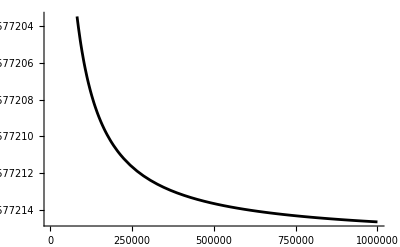

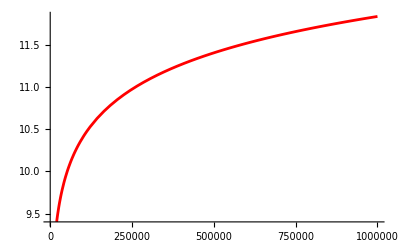

```mathematica
above=1000000;
fstapprox =Plot[(t(-g-ProductLog[ -g Exp[-g+1/(t g)]]Exp[ProductLog[ -g Exp[-g+1/(t g)]]-ProductLog[ -g Exp[-g+1/(t g^2)]]])+Log[t]/Log[g])/.{g->0.2},{t,1000,above}];
sndapprox=Plot[(t(-g-ProductLog[ -g Exp[-g+1/(t g)]]Exp[ProductLog[ -g Exp[-g+1/(t g)]]-ProductLog[ -g Exp[-g+1/(t g^2)]]Exp[ProductLog[ -g Exp[-g+1/(t g^2)]]-ProductLog[ -g Exp[-g+1/(t g^3)]]]])-Log[t]/Log[g])/.{g->0.2},{t,1000,above},PlotStyle->Red];
trdapprox=Plot[(t(-g-ProductLog[ -g Exp[-g+1/(t g)]]Exp[ProductLog[ -g Exp[-g+1/(t g)]]-ProductLog[ -g Exp[-g+1/(t g^2)]]Exp[ProductLog[ -g Exp[-g+1/(t g^2)]]-ProductLog[ -g Exp[-g+1/(t g^3)]]Exp[ProductLog[ -g Exp[-g+1/(t g^3)]]-ProductLog[ -g Exp[-g+1/(t g^4)]]]]])+Log[t]/Log[g])/.{g->0.2},{t,1000,above},PlotStyle->Yellow];
fthapprox=Plot[(t(-g-ProductLog[ -g Exp[-g+1/(t g)]]Exp[ProductLog[ -g Exp[-g+1/(t g)]]-ProductLog[ -g Exp[-g+1/(t g^2)]]Exp[ProductLog[ -g Exp[-g+1/(t g^2)]]-ProductLog[ -g Exp[-g+1/(t g^3)]]Exp[ProductLog[ -g Exp[-g+1/(t g^3)]]-ProductLog[ -g Exp[-g+1/(t g^4)]]Exp[ProductLog[ -g Exp[-g+1/(t g^4)]]-ProductLog[ -g Exp[-g+1/(t g^5)]]]]]])-Log[t]/Log[g])/.{g->0.2},{t,1000,above},PlotStyle->Orange];
EIc = Plot[-ExpIntegralEi[-1/z]-Log[z],{z,1000,above},PlotStyle->Black]

Show[sndapprox,EIc]
```

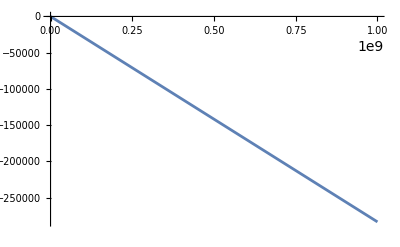

```mathematica
above=1000000000;
efstapprox =Plot[(t(-g+g Exp[-g+1/( t g)+g Exp[-g+1/(g^2 t)+g Exp[-g+1/(g^3 t)+g Exp[-g+1/(g^4 t)]]]])+ Log[t]/Log[g]) /.{g->0.2},{t,1000,above}];
Show[efstapprox]
```

General::munfl: Exp[-7648.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15297.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-30594.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

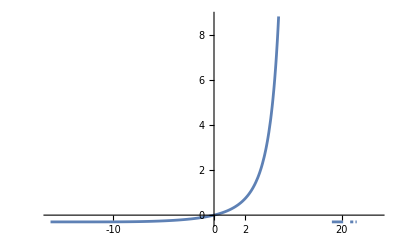

```mathematica
Plot[(-g-ProductLog[ -g Exp[-g+(t b)]]Exp[ProductLog[ -g Exp[-g+(t b)]]-ProductLog[ -g Exp[-g+(t b^2)]]Exp[ProductLog[ -g Exp[-g+(t b^2)]]-ProductLog[ -g Exp[-g+(t b^3)]]Exp[ProductLog[ -g Exp[-g+(t b^3)]]-ProductLog[ -g Exp[-g+(t b^4)]]]]])/.{g->0.3,b->0.5},{t,-Infinity,Infinity}]
```

```mathematica
Integrate[Exp[I x z-I z]Exp[-ProductLog[-g Exp[-g-I z]]],{z,-Infinity,Infinity}, Assumptions->{0<g<1}]
```

```mathematica
Integrate[z^(-1-x)ProductLog[-g Exp[-g]z],z,Assumptions->{0<g<1}]/.{z->Exp[-i z]}
```

-(ⅇ^(x ProductLog[-ⅇ^(-g-i z) g]) (ⅇ^(-i z))^-x (x Gamma[1-x,x ProductLog[-ⅇ^(-g-i z) g]]+Gamma[2-x,x ProductLog[-ⅇ^(-g-i z) g]]) (x ProductLog[-ⅇ^(-g-i z) g])^x)/x^2

```mathematica
Integrate[( -Sqrt[2( z)])Exp[I x z],{z,-Infinity,Infinity}]
```

Integrate::idiv: Integral of -√2 ⅇ^(ⅈ x z) √z does not converge on {-∞,∞}.

∫_(-∞)^∞ -√2 ⅇ^(ⅈ x z) √zⅆz

```mathematica
PowerExpand[Series[-g-ProductLog[-g Exp[-g+ x]],{x, g-1-Log[g],2}]]
```

1-g+(-1)^Floor[(π-Arg[-(ⅇ^(-1-g) (ⅇ^g-ⅇ^(1+x) g))/(-1+g-x-Log[g])]-Arg[1-g+x+Log[g]])/(2 π)] ⅈ^(6 Floor[Arg[(ⅇ^-g (-2 ⅇ^g+ⅇ^g g+ⅇ^(1+x) g-ⅇ^g x-ⅇ^g Log[g]))/(-1+g-x-Log[g])]/(2 π)]) ((11 ⅈ (x+1-g+Log[g])^(3/2))/(18 √2)+O[x+1-g+Log[g]]^(5/2))+ⅈ^(4 Floor[Arg[(ⅇ^-g (-2 ⅇ^g+ⅇ^g g+ⅇ^(1+x) g-ⅇ^g x-ⅇ^g Log[g]))/(-1+g-x-Log[g])]/(2 π)]) (-2/3 (x+1-g+Log[g])-1/3 (x+1-g+Log[g])^2+O[x+1-g+Log[g]]^3)+(-1)^Floor[(π-Arg[-(ⅇ^(-1-g) (ⅇ^g-ⅇ^(1+x) g))/(-1+g-x-Log[g])]-Arg[1-g+x+Log[g]])/(2 π)] ⅈ^(2 Floor[Arg[(ⅇ^-g (-2 ⅇ^g+ⅇ^g g+ⅇ^(1+x) g-ⅇ^g x-ⅇ^g Log[g]))/(-1+g-x-Log[g])]/(2 π)]) (-ⅈ √2 √(x+1-g+Log[g])-(ⅈ (x+1-g+Log[g])^(3/2))/(2 √2)+O[x+1-g+Log[g]]^(5/2))

```mathematica
c=0.8
r=( c-1-Log[c])
ComplexPlot[1-c- Sqrt[-2(r+I z)],{z,-0.1-0.1I, 0.1+0.1I}]
```

0.8

0.0231436

-Graphics-

```mathematica
c=0.3;
b=3;
ψ[z_] = -c  Exp[-c-I z];
Show[ComplexPlot[-c -ProductLog[ψ[b z]]Exp[ProductLog[ψ[b z]]-ProductLog[ψ[b^2 z]]Exp[ProductLog[ψ[b^2 z]]-ProductLog[ψ[b^3 z]]Exp[ProductLog[ψ[b^3 z]]-ProductLog[ψ[b^4 z]]Exp[ProductLog[ψ[b^4 z]]-ProductLog[ψ[b^5 z]]]]]], {z, -0.2 -0.1 I , 0.2+ 0.3 I }]]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

MinMax::nord: Invalid comparison with {0.3,0.3,2.79906356139296289843378414030372`15.954589196021853*^1932067995,0.3,4.0899820865942113921356682841262103`15.954442782888433*^345307669538,0.3,1.2579440091158281056996819987`15.954589770191005*^25326148132281,0.3,2.4250816026480709257438886292408976568133`15.954589770191005*^675264030563831,0.3,«134»} attempted.

$Aborted

```mathematica
c=0.3;
b=1.3;
ComplexPlot[-c -ψ[b z]Exp[-ψ[b^2 z]Exp[-ψ[b^3 z]Exp[-ψ[b^4 z]]]], {z, -2 -2 I , 2+ 2 I },PlotPoints->5,(*Reduces initial sampling points*)MaxRecursion->2  (*Prevents excessive refinement*)
,PerformanceGoal->"Speed"]
```

General::ovfl: Overflow occurred in computation.

MinMax::nord: Invalid comparison with {1.01308,1.00425,0.833989,0.584426,1.80247×10^6,6.22147,0.296604,0.317094,0.390196,0.461061,«62»} attempted.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

Image::imgarray: The specified argument Raster[<<1532561632 bytes>>] should be an array of rank 2 or 3 with machine-sized numbers.

$Aborted

```mathematica
ComplexPlot[Module[{f},f=-c-ψ[b z]Exp[-ψ[b^2 z]Exp[-ψ[b^3 z]Exp[-ψ[b^4 z]]]];
If[Abs[f]<10^5,f,10^1 Exp[I Arg[f]]] (*Cap large values but keep phase*)],{z,-1-1 I,1+1 I},PlotPoints->500,MaxRecursion->4]
```

-Graphics-

```mathematica
PowerExpand[Series[-ProductLog[ -g Exp[-g]z],{z,1,3}]]
```

g+(g (z-1))/(1-g)+((2-g) g^2 (z-1)^2)/(2 (1-g)^3)+(g^3 (9-8 g+2 g^2) (z-1)^3)/(6 (1-g)^5)+O[z-1]^4

```mathematica
PowerExpand[-(ⅇ^(x ProductLog[-ⅇ^(-g-i z) g]) (ⅇ^(-i z))^-x (x Gamma[1-x,x ProductLog[-ⅇ^(-g-i z) g]]+Gamma[2-x,x ProductLog[-ⅇ^(-g-i z) g]]) (x ProductLog[-ⅇ^(-g-i z) g])^x)/x^2/.{z->0}]
```

-(-1)^x ⅇ^(-g x) g^x x^(-2+x) (x Gamma[1-x,-g x]+Gamma[2-x,-g x])

```mathematica
Plot[(-(-1)^x ⅇ^(-g x) g^x x^(-2+x) (x Gamma[1-x,-g x]+Gamma[2-x,-g x]))/.{g->0.7},{x,-1,10}]
```

-Graphics-